# New Algorithms for Simulating Dynamical Friction of Ions in a Magnetized Electron Beam

## David L. Bruhwiler, Stephen D. Webb, Dan T. Abell RadiaSoft, LLC

## Preamble

### Constants, Indexing, Etc.

#### Physical constants

```mathematica
CLight=QuantityMagnitude@UnitConvert[
Quantity[1,"SpeedOfLight"],
Quantity[1,"Meters"]/Quantity[1 "Seconds"]
]
```

299792458

```mathematica
Qe=QuantityMagnitude@UnitConvert[
Quantity[1,"ElementaryCharge"],
"Coulombs"
]
```

1.602177×10^-19

```mathematica
ε0=QuantityMagnitude@UnitConvert[
Quantity[1.,"ElectricConstant"],
Quantity[1,"Farads"]/Quantity[1,"Meters"]
]
```

8.85419×10^-12

```mathematica
μ0=QuantityMagnitude@UnitConvert[
Quantity[1.,"MagneticConstant"],
Quantity[1,"Henries"]/Quantity[1,"Meters"]
]
```

1.25664×10^-6

```mathematica
MassE=QuantityMagnitude@UnitConvert[
Quantity[1.,"ElectronMass"],
Quantity[1,"Kilograms"]
]
```

9.10938×10^-31

```mathematica
MassP=QuantityMagnitude@UnitConvert[
Quantity[1.,"ProtonMass"],
Quantity[1,"Kilograms"]
]
```

1.67262×10^-27

```mathematica
kB=QuantityMagnitude@UnitConvert[
Quantity[1.,"BoltzmannConstant"],
Quantity[1,"Joules"]/Quantity[1,"Kelvins"]
]
```

1.38065×10^-23

#### Indexing

```mathematica
{Ix,Ipx,Iy,Ipy,Iz,Ipz}=Range[6]
```

{1,2,3,4,5,6}

#### Prefixes

```mathematica
{
femto,pico,nano,micro,milli,
one,
kilo,mega,giga,tera,peta
}=1. 10^Range[-15,15,3]
```

{1.×10^-15,1.×10^-12,1.×10^-9,1.×10^-6,0.001,1.,1000.,1.×10^6,1.×10^9,1.×10^12,1.×10^15}

### Functions

#### Utility functions

Larmor frequency

```mathematica
LarmorΩ[m_,B_,Z_:1]:= Z Qe B/m
```

Convert to guiding-center coördinates

```mathematica
toGuidingCenter[B_,Ze_]:=Module[
{mω,Zgc},
mω=MassE LarmorΩ[MassE,B,-1];
Zgc=Ze;
Zgc⟦Ix⟧=ArcTan[Ze⟦Ipy⟧,Ze⟦Ipx⟧+mω Ze⟦Iy⟧];
Zgc⟦Ipx⟧=1/(2mω)((Ze⟦Ipx⟧+mω Ze⟦Iy⟧)^2+Ze⟦Ipy⟧^2);
Zgc⟦Iy⟧=-Ze⟦Ipx⟧/mω;
Zgc⟦Ipy⟧=Ze⟦Ipy⟧+mω Ze⟦Ix⟧;
Zgc
]
```

Convert from guiding-center coördinates

```mathematica
fromGuidingCenter[B_,Zgc_]:=Module[
{mω,RL,Ze},
mω=MassE LarmorΩ[MassE,B,-1];
RL=√(2mω Zgc⟦Ipx⟧)/mω;
Ze=Zgc;
Ze⟦Ix⟧=Zgc⟦Ipy⟧/mω-RL Cos[Zgc⟦Ix⟧];
Ze⟦Ipx⟧=-mω Zgc⟦Iy⟧;
Ze⟦Iy⟧=Zgc⟦Iy⟧+RL Sin[Zgc⟦Ix⟧];
Ze⟦Ipy⟧=mω RL Cos[Zgc⟦Ix⟧];
Ze
]
```

Action J(Z_gc) using guiding-center coördinates

```mathematica
ActionJ[ZQion_,Mion_, B_,Zion_,Zgc_]:=Module[
{g,ω,mω,RL,numer,denom},
g=ZQion Qe^2/(4π ε0);
ω=LarmorΩ[MassE,B,-1];
mω=MassE ω;
RL=√(2mω Zgc⟦Ipx⟧)/mω;
numer=((Zion⟦Ix⟧-Zgc⟦Ipy⟧/mω)Cos[Zgc⟦Ix⟧]-(Zion⟦Iy⟧-Zgc⟦Iy⟧)Sin[Zgc⟦Ix⟧]);
denom=((Zion⟦Ix⟧-Zgc⟦Ipy⟧/mω)^2+(Zion⟦Iy⟧-Zgc⟦Iy⟧)^2+(Zion⟦Iz⟧-Zgc⟦Iz⟧)^2+RL^2)^(3/2);
Zgc⟦Ipx⟧+g RL/ω numer/denom
]
```

```mathematica
minImpactParam[ZQion_,B_,EVOverEK_,RLOverB_,tanα_:5,Ngyro_:100]:=Module[
{numer,denom},
numer=ZQion MassE/(4π ε0);
denom=EVOverEK/2(RLOverB^2+(tanα/(Ngyro π))^2)B^2;
(numer/denom)^(1/3)
]
```

Matrix that transforms ion coördinate-velocity data to canonically conjugate phase-space variables:

```mathematica
IonQVtoQP[Mion_]:=Module[
{mat},
mat=IdentityMatrix[6];
Do[mat⟦i,i⟧=Mion,{i,{Ipx,Ipy,Ipz}}];
mat
]
```

Matrix that transforms electron coördinate-velocity data to canonically conjugate phase-space variables:

```mathematica
ElectronQVtoQP[B_]:=Module[
{mat},
mat=IdentityMatrix[6];
Do[mat⟦i,i⟧=MassE,{i,{Ipx,Ipy,Ipz}}];
mat⟦Ipx,Iy⟧=(-Qe)(-B);
mat
]
```

#### Transfer maps

Matrix for a linear drift:

```mathematica
MatD[m_,h_]:=Module[
{Mdrift},
Mdrift=IdentityMatrix[6];
Do[Mdrift⟦i,i+1⟧=h/m,{i,{Ix,Iy,Iz}}];
Mdrift
]
```

Matrix for linear electron dynamics in a solenoidal field:

```mathematica
MatK0e[B_,h_]:=Module[
{ω,mω,ωh,cωh,sωh,cωh1m,MK0},
ω=LarmorΩ[MassE,B,-1];
mω=MassE ω;
ωh=ω h;
cωh=Cos[ωh];
sωh=Sin[ωh];
cωh1m=2 Sin[ωh/2]^2;(* 1 - Cos[α] = 2 Sin[α/2]^2 *)
MK0=IdentityMatrix[6];
MK0⟦Iy,Iy⟧=cωh;
MK0⟦Ipy,Ipy⟧=cωh;
MK0⟦Iy,Ipy⟧=sωh/mω;
MK0⟦Ipy,Iy⟧=-mω sωh;
MK0⟦Iz,Ipz⟧=h/MassE;
MK0⟦Ix,Ipx⟧=sωh/mω;
MK0⟦Ix,Iy⟧=sωh;
MK0⟦Ix,Ipy⟧=cωh1m/mω;
MK0⟦Iy,Ipx⟧=-cωh1m/mω;
MK0⟦Ipy,Ipx⟧=-sωh;
MK0
]
```

Map for ion-electron interaction:

```mathematica
MapZC[ZQion_,Mion_,h_,Zion_,Zelec_]:=Module[
{g,dZ,denom,ZFion,ZFelec},
g=h (ZQion Qe^2)/(4π ε0);
dZ=Zion-Zelec;
denom=(dZ⟦Ix⟧^2+dZ⟦Iy⟧^2+dZ⟦Iz⟧^2)^(3/2);
ZFion=Zion;
ZFelec=Zelec;
Do[
ZFion⟦ip⟧=Zion⟦ip⟧-g dZ⟦ip-1⟧/denom;
ZFelec⟦ip⟧=Zelec⟦ip⟧+g dZ⟦ip-1⟧/denom;,
{ip,{Ipx,Ipy,Ipz}}
];
{ZFion,ZFelec}
]
```

Second-order split-operator explicit integration for the total Hamiltonian

```mathematica
MapZ[ZQion_,Mion_,B_,h_,ns_,Zion_,Zelec_]:=Module[
{hh,matIon,matElec,ZTion,ZTelec,ZFion,ZFelec},
hh=h/2;
matIon=MatD[Mion,hh];
matElec=MatK0e[B,hh];
ZTion=Zion;
ZTelec=Zelec;
ZFion={Zion};
ZFelec={Zelec};
Do[
ZTion=matIon.ZTion;
ZTelec=matElec.ZTelec;
{ZTion,ZTelec}=MapZC[ZQion,Mion,h,ZTion,ZTelec];
ZTelec=matElec.ZTelec;
ZTion=matIon.ZTion;
AppendTo[ZFion,ZTion];
AppendTo[ZFelec,ZTelec];,
{ns}
];
{ZFion,ZFelec}
]
```

Map for ion-electron interaction in guiding-center coördinates:

```mathematica
MapZgcC[ZQion_,Mion_,B_,h_,Zion_,Zgc_]:=Module[
{g,mω,dR3,Ωgc,S,C1,ZFion, ZFelec,Dxgc,Dygc,Dpz},
g=ZQion Qe^2/(4π ε0);
mω=MassE LarmorΩ[MassE,B,-1];
dR3=((Zion⟦Ix⟧-Zgc⟦Ipy⟧/mω)^2+(Zion⟦Iy⟧-Zgc⟦Iy⟧)^2+(Zion⟦Iz⟧-Zgc⟦Iz⟧)^2+2/mω ActionJ[ZQion,Mion, B,Zion,Zgc])^(3/2);
Ωgc=(g/mω)/dR3;
S=Sin[Ωgc h];
C1=2 Sin[Ωgc(h/2)]^2;
ZFion=Zion;
ZFelec=Zgc;
Dxgc=(Zion⟦Ix⟧-Zgc⟦Ipy⟧/mω)C1+(Zion⟦Iy⟧-Zgc⟦Iy⟧)S;
Dygc=(Zion⟦Iy⟧-Zgc⟦Iy⟧)C1-(Zion⟦Ix⟧-Zgc⟦Ipy⟧/mω)S;
Dpz=(Ωgc h)mω(Zion⟦Iz⟧-Zgc⟦Iz⟧);
ZFion⟦Ipx⟧+=mω Dygc;
ZFion⟦Ipy⟧-=mω Dxgc;
ZFion⟦Ipz⟧-=Dpz;
ZFelec⟦Iy⟧+=Dygc;
ZFelec⟦Ipy⟧+=mω Dxgc;
ZFelec⟦Ipz⟧+=Dpz;
{ZFion,ZFelec}
]
```

Second-order split-operator integration for the total Hamiltonian in guiding-center coördinates:

```mathematica
MapZgc[ZQion_,Mion_,B_,h_,ns_,Zion_,Zgc_]:=Module[
{hh,matIon,matElec,ZTion,ZTelec,ZFion,ZFelec},
hh=h/2;
matIon=MatD[Mion,hh];
matElec=IdentityMatrix[6];
matElec⟦Iz,Ipz⟧=hh/MassE;
ZTion=Zion;
ZTelec=Zgc;
ZFion={Zion};
ZFelec={Zgc};
Do[
ZTion=matIon.ZTion;
ZTelec=matElec.ZTelec;
{ZTion,ZTelec}=MapZgcC[ZQion,Mion,B,h,ZTion,ZTelec];
ZTelec=matElec.ZTelec;
ZTion=matIon.ZTion;
AppendTo[ZFion,ZTion];
AppendTo[ZFelec,ZTelec];,
{ns}
];
{ZFion,ZFelec}
]
```

ΔP_ion computed using the Magnus expansion:

```mathematica
MagnusΔPion[ZQion_,Mion_,B_,h_,Zion_,Zgc_]:=Module[
{g,mω,xgc,C1,C2,C3,Bdenom,Δ,D1,D2,dPx,dPy,dPz},
g=ZQion Qe^2/(4π ε0);
mω=MassE LarmorΩ[MassE,B,-1];
xgc=Zgc⟦Ipy⟧/mω;
C1=(Zion⟦Ix⟧-xgc)^2+(Zion⟦Iy⟧-Zgc⟦Iy⟧)^2+(Zion⟦Iz⟧-Zgc⟦Iz⟧)^2+2/mω ActionJ[ZQion,Mion, B,Zion,Zgc];
C2=2((Zion⟦Ix⟧-xgc)Zion⟦Ipx⟧/Mion+(Zion⟦Iy⟧-Zgc⟦Iy⟧)Zion⟦Ipy⟧/Mion+(Zion⟦Iz⟧-Zgc⟦Iz⟧)(Zion⟦Ipz⟧/Mion-Zgc⟦Ipz⟧/MassE));
C3=((Zion⟦Ipx⟧/Mion)^2+(Zion⟦Ipy⟧/Mion)^2+(Zion⟦Ipz⟧/Mion-Zgc⟦Ipz⟧/MassE)^2);
Bdenom=√(C1+(C2+C3 h)h);
Δ=4C1 C3-C2^2;
D1=(2C3 h+C2)/Bdenom-C2/(√C1);
D2=(C2 h+2C1)/Bdenom-2 √C1;
dPx=-(2g)/Δ((Zion⟦Ix⟧-xgc)D1-Zion⟦Ipx⟧/Mion D2);
dPy=-(2g)/Δ((Zion⟦Iy⟧-Zgc⟦Iy⟧)D1-Zion⟦Ipy⟧/Mion D2);
dPz=-(2g)/Δ((Zion⟦Iz⟧-Zgc⟦Iz⟧)D1-(Zion⟦Ipz⟧/Mion-Zgc⟦Ipz⟧/MassE)D2);
{dPx,dPy,dPz}
]
```

#### Error computation

```mathematica
(* relErrAvging[ZQion_,Mion_,B_,EVOverEK_,RLOverB_,tanα_:5,Ngyro_:100]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,
Zion,Zelec,Zgce,ZFion,ZFelec,ZFgci,ZFgce,dPexp,dPavg},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@Tintxn/dTe;
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec=Transpose@{{0.,Vperp,bParam-RL,0.,-Lintxn,Vz}};
Zelec=ElectronQVtoQP[B].Zelec;
Zgce=toGuidingCenter[B,Zelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,Zion,Zelec];
{ZFgci,ZFgce}=MapZgc[ZQion,Mion,B,,NSPerGyro dTe,numSteps/NSPerGyro,Zion,Zgce];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPavg=Transpose@(ZFgci⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFgci⟦1,{Ipx,Ipy,Ipz},;;⟧);
(Norm/@(dPavg-dPexp))/(Norm/@dPexp)
]*)
```

```mathematica
relErrAvging[ZQion_,Mion_,B_,EVOverEK_,RLOverB_,tanα_:5,Ngyro_:100,nAvg_:1]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,
Zion,Zelec,Zgce,ZFion,ZFelec,ZFgci,ZFgce,dPexp,dPavg},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@(Tintxn/dTe);
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec=Transpose@{{0.,Vperp,bParam-RL,0.,-Lintxn,Vz}};
Zelec=ElectronQVtoQP[B].Zelec;
Zgce=toGuidingCenter[B,Zelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,Zion,Zelec];
{ZFgci,ZFgce}=MapZgc[ZQion,Mion,B,,nAvg NSPerGyro dTe,numSteps/(nAvg NSPerGyro),Zion,Zgce];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPavg=Transpose@(ZFgci⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFgci⟦1,{Ipx,Ipy,Ipz},;;⟧);
(Norm/@(dPavg-dPexp))/(Norm/@dPexp)
]
```

```mathematica
relErrMagnus[ZQion_,Mion_,B_,EVOverEK_,RLOverB_,tanα_:5,Ngyro_:100]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,
Zion,Zelec,Zgce,ZFion,ZFelec,dPexp,dPmgn},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@(Tintxn/dTe);
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec=Transpose@{{0.,Vperp,bParam-RL,0.,-Lintxn,Vz}};
Zelec=ElectronQVtoQP[B].Zelec;
Zgce=toGuidingCenter[B,Zelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,Zion,Zelec];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPmgn=Transpose@MagnusΔPion[ZQion,Mion,B,Tintxn,Zion,Zgce];
(Norm/@(dPmgn-dPexp))/(Norm/@dPexp)
]
```

```mathematica
(* relErrAvging[ZQion_,Mion_,B_,EVOverEK_?VectorQ,RLOverB_,tanα_:5,Ngyro_:100]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,zeroes,
Zion,Zelec,nI0,nE0,ZIion,ZIelec,ZIgce,ZFion,ZFelec,ZFgci,ZFgce,dPexp,dPavg},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@Tintxn/dTe;
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
zeroes=Table[0.,Length[EVOverEK]];
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec={zeroes,Vperp,bParam-RL,zeroes,-Lintxn,Vz};
Zelec=ElectronQVtoQP[B].Zelec;
nI0=Dimensions[Zion]⟦2⟧;
nE0=Dimensions[Zelec]⟦2⟧;
ZIion=Zion⟦;;,1+Floor[Range[0,nI0 nE0-1]/nE0]⟧;
ZIelec=Join[Sequence@@Table[Zelec,nI0],2];
ZIgce=toGuidingCenter[B,ZIelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,ZIion,ZIelec];
{ZFgci,ZFgce}=MapZgc[ZQion,Mion,B,NSPerGyro dTe,numSteps/NSPerGyro,ZIion,ZIgce];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPavg=Transpose@(ZFgci⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFgci⟦1,{Ipx,Ipy,Ipz},;;⟧);
(Norm/@(dPavg-dPexp))/(Norm/@dPexp)
]*)
```

```mathematica
relErrAvging[ZQion_,Mion_,B_,EVOverEK_?VectorQ,RLOverB_,tanα_:5,Ngyro_:100,nAvg_:1]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,zeroes,
Zion,Zelec,nI0,nE0,ZIion,ZIelec,ZIgce,ZFion,ZFelec,ZFgci,ZFgce,dPexp,dPavg},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@(Tintxn/dTe);
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
zeroes=Table[0.,Length[EVOverEK]];
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec={zeroes,Vperp,bParam-RL,zeroes,-Lintxn,Vz};
Zelec=ElectronQVtoQP[B].Zelec;
nI0=Dimensions[Zion]⟦2⟧;
nE0=Dimensions[Zelec]⟦2⟧;
ZIion=Zion⟦;;,1+Floor[Range[0,nI0 nE0-1]/nE0]⟧;
ZIelec=Join[Sequence@@Table[Zelec,nI0],2];
ZIgce=toGuidingCenter[B,ZIelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,ZIion,ZIelec];
{ZFgci,ZFgce}=MapZgc[ZQion,Mion,B,nAvg NSPerGyro dTe,numSteps/(nAvg NSPerGyro),ZIion,ZIgce];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPavg=Transpose@(ZFgci⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFgci⟦1,{Ipx,Ipy,Ipz},;;⟧);
(Norm/@(dPavg-dPexp))/(Norm/@dPexp)
]
```

```mathematica
relErrMagnus[ZQion_,Mion_,B_,EVOverEK_?VectorQ,RLOverB_,tanα_:5,Ngyro_:100]:=Module[
{NSPerGyro,g,ωe,Te,dTe,Tintxn,numSteps,bParam,RL,Lintxn,Vperp,Vz,zeroes,
Zion,Zelec,nI0,nE0,ZIion,ZIelec,ZIgce,ZFion,ZFelec,dPexp,dPmgn},
NSPerGyro=40;
g=ZQion Qe^2/(4π ε0);
ωe=LarmorΩ[MassE,B,-1];
Te=(2π)/Abs[ωe];
dTe=Te/NSPerGyro;
Tintxn=Ngyro Te;(* full interaction time *)
numSteps=Round@(Tintxn/dTe);
bParam=(g (2/(EVOverEK MassE))/((RLOverB ωe)^2+((2 tanα)/(Ngyro Te))^2))^(1/3);
RL=bParam RLOverB;
Lintxn=bParam tanα;(* half-length *)
Vperp=-RL ωe;
Vz=(2Lintxn)/Tintxn;
zeroes=Table[0.,Length[EVOverEK]];
Zion=Transpose@{{0.,0.,0.,0.,0.,0.}};
Zion=IonQVtoQP[Mion].Zion;
Zelec={zeroes,Vperp,bParam-RL,zeroes,-Lintxn,Vz};
Zelec=ElectronQVtoQP[B].Zelec;
nI0=Dimensions[Zion]⟦2⟧;
nE0=Dimensions[Zelec]⟦2⟧;
ZIion=Zion⟦;;,1+Floor[Range[0,nI0 nE0-1]/nE0]⟧;
ZIelec=Join[Sequence@@Table[Zelec,nI0],2];
ZIgce=toGuidingCenter[B,ZIelec];
{ZFion,ZFelec}=MapZ[ZQion,Mion,B,dTe,numSteps,ZIion,ZIelec];
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPmgn=Transpose@MagnusΔPion[ZQion,Mion,B,Tintxn,ZIion,ZIgce];
(Norm/@(dPmgn-dPexp))/(Norm/@dPexp)
]
```

## Explore a Range of Perturbation Parameters

```mathematica
Qion=1;
Mion=MassP;
eTemp=300.;(* Kelvin *)
magB=1.; (* Tesla *)

Ngyro=100; (* to enforce adequate averaging *)
tanα=5.0; (* to ensure an adequate opening angle *)
```

```mathematica
(ωe=LarmorΩ[MassE,magB,-1])/giga
(Te=(2π)/Abs[ωe])/pico
(Vth=√((2kB eTemp)/MassE))/kilo
(Rgc=(MassE Vth)/(Qe magB))/micro
```

-175.882

35.7239

95.3614

0.54219

```mathematica
RLvsB=1/20.;(* 20 == max perturbation ratio of about 0.1 *)
EVvsEK=1/10.;
minImpactParam[Qion,magB,EVvsEK,RLvsB]/micro
```

3.90333

```mathematica
decades=2;
ptsPerDecade=32;
logBs=Range[0.,decades,1/ptsPerDecade];
impactParameterB=(10^logBs)micro ;
impactParameterB/micro
```

{1.,1.07461,1.15478,1.24094,1.33352,1.43301,1.53993,1.65482,1.77828,1.91095,2.05353,2.20673,2.37137,2.5483,2.73842,2.94273,3.16228,3.39821,3.65174,3.92419,4.21697,4.53158,4.86968,5.23299,5.62341,6.04296,6.49382,6.97831,7.49894,8.05842,8.65964,9.30572,10.,10.7461,11.5478,12.4094,13.3352,14.3301,15.3993,16.5482,17.7828,19.1095,20.5353,22.0673,23.7137,25.483,27.3842,29.4273,31.6228,33.9821,36.5174,39.2419,42.1697,45.3158,48.6968,52.3299,56.2341,60.4296,64.9382,69.7831,74.9894,80.5842,86.5964,93.0572,100.}

```mathematica
LarmorR=impactParameterB RLvsB;
Vperp=-LarmorR ωe;
Lintxn=tanα impactParameterB;
Vz=(2Lintxn)/(Ngyro Te);
Tintxn=(2Lintxn)/Vz;
numStepsPerGyro=40;
dTe=Te/numStepsPerGyro;
Tintxn/dTe
numSteps=Round@(Tintxn/dTe)⟦1⟧
```

{4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.,4000.}

4000

```mathematica
eVca=(Qion Qe^2)/(4π ε0)/impactParameterB;
Ekin=MassE/2(Vperp^2+Vz^2);
eVcaOverEkin=eVca/Ekin
```

{5.94712,4.79244,3.86195,3.11212,2.50788,2.02095,1.62857,1.31237,1.05756,0.852229,0.686762,0.553422,0.445971,0.359382,0.289605,0.233376,0.188064,0.15155,0.122126,0.0984139,0.0793061,0.0639082,0.0514999,0.0415008,0.0334431,0.0269499,0.0217173,0.0175007,0.0141028,0.0113647,0.00915812,0.00738,0.00594712,0.00479244,0.00386195,0.00311212,0.00250788,0.00202095,0.00162857,0.00131237,0.00105756,0.000852229,0.000686762,0.000553422,0.000445971,0.000359382,0.000289605,0.000233376,0.000188064,0.00015155,0.000122126,0.0000984139,0.0000793061,0.0000639082,0.0000514999,0.0000415008,0.0000334431,0.0000269499,0.0000217173,0.0000175007,0.0000141028,0.0000113647,9.15812×10^-6,7.38×10^-6,5.94712×10^-6}

```mathematica
QVtoZion=IonQVtoQP[Mion];
QVtoZelec=ElectronQVtoQP[magB];
```

```mathematica
QVion=Transpose@{{0.0Rgc,0.000Vth,0.0Rgc,0.000Vth,0.0,0.000Vth}};
Zion=QVtoZion.QVion;
```

```mathematica
QVelec={
Table[0.,Evaluate@Dimensions[impactParameterB]],
Vperp,
impactParameterB-LarmorR,
Table[0.,Evaluate@Dimensions[impactParameterB]],
-Lintxn,
Lintxn Abs[ωe]/(Ngyro π)
};
Zelec=QVtoZelec.QVelec;
```

```mathematica
nIon0=Dimensions[Zion]⟦2⟧;
nElec0=Dimensions[Zelec]⟦2⟧;
```

```mathematica
ZIelec=Join[Sequence@@Table[Zelec,nIon0],2];
ZIion=Zion⟦;;,1+Floor[Range[0,nIon0 nElec0-1]/nElec0]⟧;
```

```mathematica
nIon=Dimensions[ZIion]⟦2⟧;
nElec=Dimensions[ZIelec]⟦2⟧;
```

```mathematica
{ZFion,ZFelec}=MapZ[Qion,Mion,magB,dTe,numSteps,ZIion,ZIelec];
```

```mathematica
ZIgce=toGuidingCenter[magB,ZIelec];
```

```mathematica
{ZFgci,ZFgce}=MapZgc[Qion,Mion,magB,numStepsPerGyro dTe,numSteps/numStepsPerGyro,ZIion,ZIgce];
```

```mathematica
dPexp=Transpose@(ZFion⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFion⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPavg=Transpose@(ZFgci⟦-1,{Ipx,Ipy,Ipz},;;⟧-ZFgci⟦1,{Ipx,Ipy,Ipz},;;⟧);
dPmgn=Transpose@MagnusΔPion[Qion,Mion,magB,Tintxn,ZIion,ZIgce];
```

```mathematica
relErrAvg=(Norm/@(dPavg-dPexp))/(Norm/@dPexp)
relErrMgn=(Norm/@(dPmgn-dPexp))/(Norm/@dPexp)
```

{0.0139404,0.0159505,0.0100426,0.0261711,0.00576109,0.00539491,0.00466947,0.0041367,0.00370134,0.0033507,0.00307415,0.00285843,0.00269317,0.00256955,0.00248012,0.00241859,0.00237951,0.00235818,0.00235049,0.0023529,0.00236237,0.00237636,0.00239287,0.00241032,0.0024276,0.00244396,0.00245892,0.00247227,0.00248395,0.002494,0.00250254,0.00250972,0.00251572,0.00252068,0.00252478,0.00252814,0.00253088,0.00253312,0.00253495,0.00253643,0.00253763,0.0025386,0.00253939,0.00254002,0.00254054,0.00254095,0.00254129,0.00254156,0.00254178,0.00254195,0.00254209,0.00254221,0.0025423,0.00254237,0.00254243,0.00254248,0.00254252,0.00254255,0.00254258,0.0025426,0.00254262,0.00254263,0.00254264,0.00254265,0.00254265}

{1.79242,1.53141,1.31449,2.35968,2.5464,2.31279,2.05617,1.81053,1.58406,1.37865,1.19412,1.02947,0.883409,0.754522,0.641384,0.5426,0.456827,0.382778,0.319229,0.265016,0.219044,0.180289,0.1478,0.120708,0.0982257,0.0796507,0.0643638,0.051826,0.0415733,0.0332105,0.0264037,0.0208734,0.0163871,0.0127521,0.00981007,0.00743104,0.00550883,0.00395705,0.00270575,0.00169923,0.0008969,0.000311054,0.000398342,0.00078742,0.00112227,0.00139601,0.00161788,0.00179721,0.00194198,0.00205878,0.00215298,0.00222893,0.00229016,0.00233952,0.00237931,0.00241138,0.00243722,0.00245805,0.00247484,0.00248837,0.00249927,0.00250806,0.00251514,0.00252085,0.00252545}

```mathematica
ξAvg=Transpose@{eVcaOverEkin,relErrAvg};
ξMgn=Transpose@{eVcaOverEkin,relErrMgn};
```

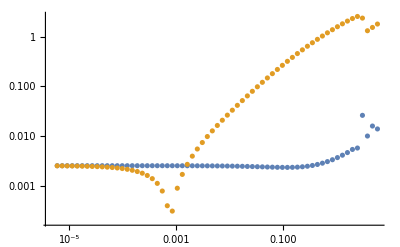

```mathematica
ListLogLogPlot[{ξAvg,ξMgn}]
```

```mathematica
decades=5;
ptsPerDecade=16;
logη=N@Range[-decades,0,1/ptsPerDecade];
eVOverEkin=10^logη;
```

```mathematica
decades=2;
ptsPerDecade=32;
logξ=N@Range[-decades-1,-1,1/ptsPerDecade];
RLOverB=10^logξ;
```

```mathematica
relErrAvg=relErrAvging[Qion,Mion,magB,eVOverEkin,#]&/@RLOverB;
```

```mathematica
relErrAvg2=relErrAvging[Qion,Mion,magB,eVOverEkin,#,5,100,2]&/@RLOverB;
```

```mathematica
relErrMgn=relErrMagnus[Qion,Mion,magB,eVOverEkin,#]&/@RLOverB;
```

```mathematica
MinMax[logη]
MinMax[logξ]
```

{-5.,0.}

{-3.,-1.}

```mathematica
MinMax@Log10@relErrAvg
MinMax@Log10@relErrAvg2
MinMax@Log10@relErrMgn
```

{-9.20228,-1.88096}

{-7.72665,-0.0669063}

{-6.47517,0.412757}

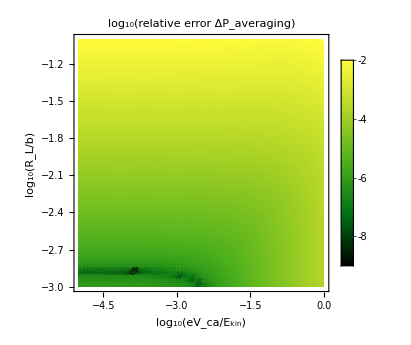

```mathematica
ListDensityPlot[Log10@relErrAvg,DataRange->{MinMax[logη],MinMax[logξ]},
ColorFunction->"AvocadoColors",
PlotRange->{-9,-2},
PlotLabel->"log_10(relative error ΔP_averaging)",
FrameLabel->{"log_10(eV_ca/E_kin)","log_10(R_L/b)"},
PlotLegends->Automatic,
BaseStyle->{FontFamily->"Palatino",FontSize->14},
ImageSize->345
]
```

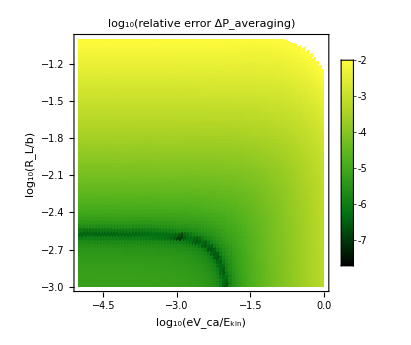

```mathematica
ListDensityPlot[Log10@relErrAvg2,DataRange->{MinMax[logη],MinMax[logξ]},
ColorFunction->"AvocadoColors",
PlotRange->{-8,-2},
PlotLabel->"log_10(relative error ΔP_averaging)",
FrameLabel->{"log_10(eV_ca/E_kin)","log_10(R_L/b)"},
PlotLegends->Automatic,
BaseStyle->{FontFamily->"Palatino",FontSize->14},
ImageSize->345
]
```

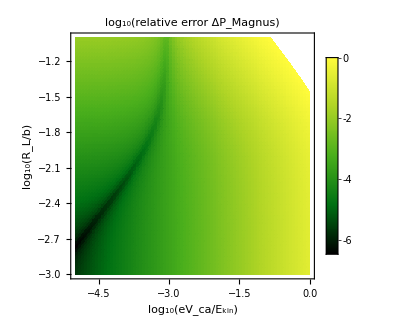

```mathematica
ListDensityPlot[Log10@relErrMgn,DataRange->{MinMax[logη],MinMax[logξ]},
ColorFunction->"AvocadoColors",
PlotRange->{-6.5,0.},
PlotLabel->"log_10(relative error ΔP_Magnus)",
FrameLabel->{"log_10(eV_ca/E_kin)","log_10(R_L/b)"},
PlotLegends->Automatic,
BaseStyle->{FontFamily->"Palatino",FontSize->14},
ImageSize->330
]
```

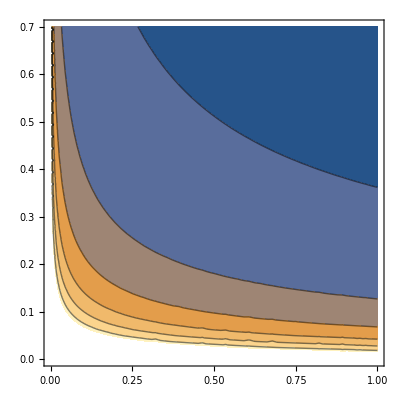

```mathematica
ContourPlot[minImpactParam[Qion,magB,eVEK,RB]/micro,{eVEK,0,1},{RB,0,0.7}]
```

```mathematica
ListDensityPlot[Log10@relErrMgn,DataRange->{MinMax[logη],MinMax[logξ]},
ColorFunction->"AvocadoColors",
PlotRange->{-6.5,0.},
PlotLabel->"log_10(relative error ΔP_Magnus)",
FrameLabel->{"log_10(eV_ca/E_kin)","log_10(R_L/b)"},
PlotLegends->Automatic,
BaseStyle->{FontFamily->"Palatino",FontSize->12},
ImageSize->345,
Epilog->{ Darker@Red}
]
```